```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 184 Kb

{Utilities`CleanSlate`,Parallel`Debug`Perfmon`,Parallel`Debug`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Clear[r] 
r = { ys[t] + l Sin[θ[t]] , - l Cos[θ[t]] }
```

{l Sin[θ[t]]+ys[t],-l Cos[θ[t]]}

```mathematica
D[r, t]
```

{ys'[t]+l Cos[θ[t]] θ'[t],l Sin[θ[t]] θ'[t]}

```mathematica
D[r, t] . D[r, t]
```

l^2 Sin[θ[t]]^2 θ'[t]^2+(ys'[t]+l Cos[θ[t]] θ'[t])^2

```mathematica
D[r, t] . D[r, t]  // Expand
```

ys'[t]^2+2 l Cos[θ[t]] ys'[t] θ'[t]+l^2 Cos[θ[t]]^2 θ'[t]^2+l^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[r, t] . D[r, t]  // Expand  // Simplify
```

ys'[t]^2+2 l Cos[θ[t]] ys'[t] θ'[t]+l^2 θ'[t]^2

```mathematica
Clear[T] 
T = 1/2 m ( D[r, t] . D[r, t]  // Expand  // Simplify  )
```

1/2 m (ys'[t]^2+2 l Cos[θ[t]] ys'[t] θ'[t]+l^2 θ'[t]^2)

```mathematica
Clear[V]
V = - m g l Cos[θ[t]]
```

-g l m Cos[θ[t]]

```mathematica
Clear[ℒ]
ℒ = T - V
```

g l m Cos[θ[t]]+1/2 m (ys'[t]^2+2 l Cos[θ[t]] ys'[t] θ'[t]+l^2 θ'[t]^2)

```mathematica
Clear[q] 
q = { ys[t] , θ[t] }
```

{ys[t],θ[t]}

```mathematica
Expand[D[ D[ ℒ , D[q[[1]], t] ] , t ] - D[ ℒ , q[[1]] ]] // Simplify 
Expand[D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ]]  // Simplify
```

m (-l Sin[θ[t]] θ'[t]^2+ys''[t]+l Cos[θ[t]] θ''[t])

l m (g Sin[θ[t]]+Cos[θ[t]] ys''[t]+l θ''[t])

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

m (l Sin[θ[t]] θ'[t]^2-ys''[t]-l Cos[θ[t]] θ''[t])==0
-l m (g Sin[θ[t]]+Cos[θ[t]] ys''[t]+l θ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
m-> 200 , 
l-> 0.5 , 
g-> 9.8 
} ;
parameters // TableForm
```

m→200
l→0.5
g→9.8

```mathematica
eqs /. parameters // TableForm
```

200 (0.5 Sin[θ[t]] θ'[t]^2-ys''[t]-0.5 Cos[θ[t]] θ''[t])==0
-100. (9.8 Sin[θ[t]]+Cos[θ[t]] ys''[t]+0.5 θ''[t])==0

```mathematica
Clear[ics]
ics = { 
θ[0] == π/3 ,
θ'[0] == 0 , 
ys[0] == 0 ,
ys'[0] == 0.005 
} ;
ics // TableForm
```

θ[0]==π/3
θ'[0]==0
ys[0]==0
ys'[0]==0.005

```mathematica
Clear[solution]
solution = 
NDSolve[ Union[ eqs /. parameters , ics ] , q , { t , 0 , 0.224 } ]
```

{{ys[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}}

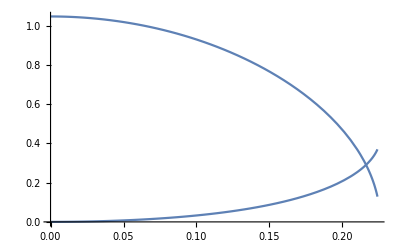

```mathematica
Plot[ q/. solution , { t, 0, 0.224 } ]
```

```mathematica
Simplify[Expand[D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ]]]
Simplify[Expand[D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ]]][[3]]
```

l m (g Sin[θ[t]]+Cos[θ[t]] ys''[t]+l θ''[t])

g Sin[θ[t]]+Cos[θ[t]] ys''[t]+l θ''[t]

```mathematica
Clear[eqa]
eqa = 
Simplify[Expand[D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ]]][[3]]  == 0
```

g Sin[θ[t]]+Cos[θ[t]] ys''[t]+l θ''[t]==0

```mathematica
Clear[ysReplace]
ysReplace = 
ys[t]-> y0 Cos[ ω t ]
```

ys[t]→y0 Cos[t ω]

```mathematica
D[D[ysReplace, t], t]
```

ys''[t]→-y0 ω^2 Cos[t ω]

```mathematica
eqa /. D[D[ysReplace, t], t]
```

-y0 ω^2 Cos[t ω] Cos[θ[t]]+g Sin[θ[t]]+l θ''[t]==0

```mathematica
Normal[Series[Sin[θ[t]] , { θ[t] , 0, 1 } ] ]
Normal[Series[Cos[θ[t]] , { θ[t] , 0, 1 } ] ]
```

θ[t]

1

```mathematica
eqa /. D[D[ysReplace, t], t] /. Sin[θ[t]] -> Normal[Series[Sin[θ[t]] , { θ[t] , 0, 1 } ] ] /.  Cos[θ[t]] -> Normal[Series[Cos[θ[t]] , { θ[t] , 0, 1 } ] ]  /. g-> ω0^2 l
```

-y0 ω^2 Cos[t ω]+l ω0^2 θ[t]+l θ''[t]==0

```mathematica
Clear[eqc]
eqc = 
eqa /. D[D[ysReplace, t], t] /. Sin[θ[t]] -> Normal[Series[Sin[θ[t]] , { θ[t] , 0, 1 } ] ] /.  Cos[θ[t]] -> Normal[Series[Cos[θ[t]] , { θ[t] , 0, 1 } ] ]  /. g-> ω0^2 l
```

-y0 ω^2 Cos[t ω]+l ω0^2 θ[t]+l θ''[t]==0

```mathematica
Clear[θReplace]
θReplace = 
θ[t] -> A Cos[ ω t ]
```

θ[t]→A Cos[t ω]

```mathematica
D[θReplace, t]
```

θ'[t]→-A ω Sin[t ω]

```mathematica
D[D[θReplace, t], t]
```

θ''[t]→-A ω^2 Cos[t ω]

```mathematica
eqc /. D[D[θReplace, t], t] /. θReplace
```

-A l ω^2 Cos[t ω]-y0 ω^2 Cos[t ω]+A l ω0^2 Cos[t ω]==0

```mathematica
Solve[
eqc /. D[D[θReplace, t], t] /. θReplace  , A ]
```

{{A→-(y0 ω^2)/(l (ω^2-ω0^2))}}